```mathematica
$HistoryLength = 0;
SetDirectory["/home/user/work/attitudeStabilization/Attitude-Stabilization-of-a-Satellite-with-Flexible-Elements/tests/saved_data"];
```

```mathematica
rotationBasisVectors = Import["rotations/basis_vector_rotation.txt", "Table"];
toBasis[ls_]:= Partition[ls,3];
rotationBasisVectors = toBasis/@rotationBasisVectors;
rotationBasisVectors
```

```mathematica
basisX = Transpose[rotationBasisVectors][[1]];
basisY = Transpose[rotationBasisVectors][[2]];
basisZ = Transpose[rotationBasisVectors][[3]];
```

```mathematica
Graphics3D[{Blue, Arrow[basisX[[;;1000]]], Green, Arrow[basisY[[;;1000]]],Red, Arrow[basisZ[[;;1000]]]}, ViewProjection->"Orthographic",Boxed->True,ImageSize->Large,Axes->True]
```

-Graphics3D-

```mathematica
Graphics3D[{Arrow[{{0, 0, 0},basisX[[1]]}]}]
```

-Graphics3D-

```mathematica
ls = ParallelTable[
Graphics3D[{
satScaledGraphics3D[sat1[[i]],500 10^3],
satScaledGraphics3D[sat2[[i]],500 10^3]
},ViewProjection->"Orthographic",Boxed->True,ImageSize->Large,Axes->True]
,
{i,1,Length[sat1],10}];


ListAnimate[ls,DisplayAllSteps->False]
```

```mathematica
gravityMomentNorm = Import["rotations/gravity_moment_norm.txt", "Table"];
```

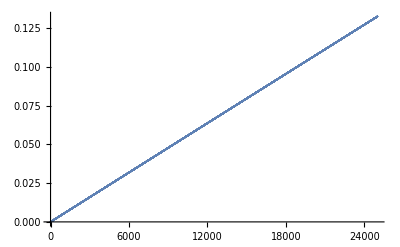

```mathematica
ListPlot[(Transpose[gravityMomentNorm[[;;25000]]] - gravityMomentNorm[[1]])/ gravityMomentNorm[[1]]]
```